## Color Picker

```mathematica
colors = {White, Green, Orange, Red, Blue, Yellow};
currentColor = Transparent;
```

```mathematica
SetColorPickerCol[color_] := Module[{},
currentColor = color;
];
```

```mathematica
GenColorPickerColBox[coord_,color_] := Module[{r},
r = Rectangle[coord];
r = Style[r,{color,EdgeForm[Thick]}];
Button[r,SetColorPickerCol[color]]
];
```

```mathematica
GenColorPickerBox[colors] := Module[{colorBox = {}},
AppendTo[colorBox,GenColorPickerColBox[{0,0},colors[[1]]]];
AppendTo[colorBox,GenColorPickerColBox[{1,0},colors[[2]]]];AppendTo[colorBox,GenColorPickerColBox[{2,0},colors[[3]]]];
AppendTo[colorBox,GenColorPickerColBox[{0,1},colors[[4]]]];
AppendTo[colorBox,GenColorPickerColBox[{1,1},colors[[5]]]];
AppendTo[colorBox,GenColorPickerColBox[{2,1},colors[[6]]]];
colorBox
];
```

```mathematica
VisualizeColorPickerBox[colors] := Module[{picker, pickerTitle, current, currentTitle, col1, col2},
currentColor = Transparent;

pickerTitle = "Color Picker";
picker = GenColorPickerBox[colors];
col1 = Column[{
Style[pickerTitle,{25,Red, Bold}],
Graphics[picker,ImageSize->Medium]
}];

currentTitle = "Current Color";
current = {Dynamic[currentColor],EdgeForm[Thick], Rectangle[]};
col2 = Column[{
Style[currentTitle,{25,Red,Bold}],
Graphics[current, ImageSize->Tiny]
}];

Print[Panel[Row[{col1,col2}]]]
];
```

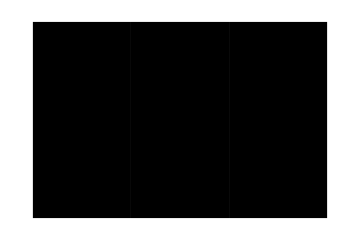
Color Picker
-Graphics-Current Color
-Graphics-

```mathematica
VisualizeColorPickerBox[colors];
```

## Canvas

```mathematica
ClickHandler[coord_] := Module[{}, 
ind = Position[c,coord][[1]][[1]];
If[ContainsAny[{5,23,26,29,32,50},{ind}]==False,
c[[ind]][[2]] = currentColor;
]
];
```

```mathematica
(* Genero un rettangolo di lato 1 con angolo in posizione coord e colore col *)
GenRect[rect_, col_] := Module[{},
Style[Rectangle[rect],{col,EdgeForm[Thick]}]
];
```

```mathematica
GenBtn[rectStr_] := Module[{coord, col},
coord = rectStr[[1]];
col = rectStr[[2]];
r = GenRect[coord,col];
Button[r,ClickHandler[coord]]
];
```

```mathematica
GenerateBaseCubeStruct[] := Module[{points = {}, defaultColor = Transparent},
	(* Genero i rettangoli del mio cubo aperto *)
	points=Join[points,Table[{{x,8},defaultColor},{x,3,5}]];
	points=Join[points,Table[{{x,7},defaultColor},{x,3,5}]];
	points=Join[points,Table[{{x,6},defaultColor},{x,3,5}]];
	points=Join[points,Table[{{x,5},defaultColor},{x,0,11}]];
	points=Join[points,Table[{{x,4},defaultColor},{x,0,11}]];
	points=Join[points,Table[{{x,3},defaultColor},{x,0,11}]];
	points=Join[points,Table[{{x,2},defaultColor},{x,3,5}]];
	points=Join[points,Table[{{x,1},defaultColor},{x,3,5}]];
	points=Join[points,Table[{{x,0},defaultColor},{x,3,5}]];

(* Imposto manualmente i colori dei centri:
 F = 26,
	B= 32,
	U = 5,
	D = 50,
	L = 23,
	R = 29	
 *)
points[[5]][[2]] =colors[[1]]; (* Up *)
points[[26]][[2]] =colors[[2]]; (* Front *)
points[[23]][[2]] =colors[[3]]; (* Left *)
points[[29]][[2]] =colors[[4]]; (* Right *)
points[[32]][[2]] =colors[[5]]; (* Back *)
points[[50]][[2]] =colors[[6]];(* Down *)
points
];
```

```mathematica
c = GenerateBaseCubeStruct[];
```

```mathematica
Panel[
Graphics[Dynamic[Map[GenBtn,c]]], Background->Gray, ImageSize->Large
]
```

-Graphics-